```mathematica
(* equazione di diffusione unidimensionale *)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
pde = D[n[x,t],t]==Dcoeff D[n[x,t],x,x] /. {Dcoeff-> 0.05}
```

n^(0,1)[x,t]==0.05 n^(2,0)[x,t]

```mathematica
(* risolviamola in un intervallo limitato con con n(0)=n(L)=0 e n(x,0) = u0 = costante *)
```

```mathematica
inifunc1[x_,L_,u0_]:=Piecewise[{{0, x== 0},{0,x==L}}, u0];
```

```mathematica
Sol[L_,u0_]:=Module[{},NDSolve[{pde, n[x,0]== inifunc1[x,L,u0],n[0,t]==0,n[L,t]==0},n[x,t],{x,0,L},{t,0,5.0},
MaxStepSize->0.1][[1,1,2]]];
```

```mathematica
nsol[x_,t_]=Sol[1,20]
```

InterpolatingFunction[{{0.,1.},{0.,5.}},<>][x,t]

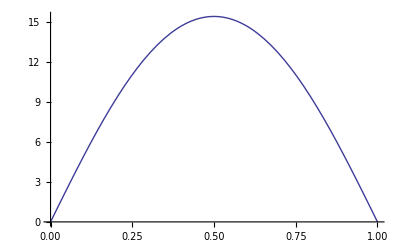

```mathematica
Plot[nsol[x,1],{x,0,1}]
```

```mathematica
Plot3D[nsol[x,t], {x,0,1},{t,0,5},PlotRange-> {0,20},AxesLabel->{x,t}]
```

-Graphics3D-

```mathematica
(* soluzione esatta *)
```

```mathematica
nexact[x_,t_,u0_,L_,D_]=4 Sum[u0/((2n+1)π)Sin[(2 n +1)π/L x] Exp[-D (2n+1)^2 π^2/L^2 t],{n,0,100}];
```

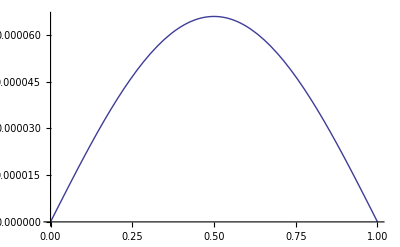

```mathematica
Plot[nexact[x,1,1,1,1],{x,0,1}]
```

```mathematica
(* confronto con soluzione numerica *)
```

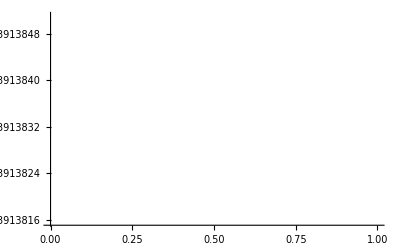

```mathematica
Plot[nsol[x,1]/ nexact[x,1,1,1,1],{x,0,1}]
```

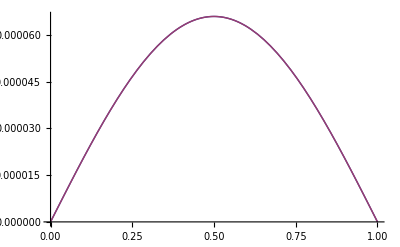

```mathematica
Plot[{nsol[x,1], nexact[x,1,1,1,1]},{x,0,1}]
```

```mathematica
(* condizione iniziale diversa (Esercizio #1) *)
```

```mathematica
(* risolviamola in un intervallo limitato con con n(0)=n(L)=0 e n(x,0) = sin( π x / L) *)
```

```mathematica
inifunc2[x_,L_,u0_]=Piecewise[{{0, x== 0},{0,x==L}}, Sin[π x /L]];
```

```mathematica
Sol2[L_,u0_]:=Module[{},NDSolve[{pde, n[x,0]== inifunc2[x,L,u0],n[0,t]==0,n[L,t]==0},n[x,t],{x,0,L},{t,0,1.0},
MaxStepSize->1/5000][[1,1,2]]];
```

```mathematica
nsol2[x_,t_]=Sol2[1,1]
```

InterpolatingFunction[{{0.,1.},{0.,1.}},<>][x,t]

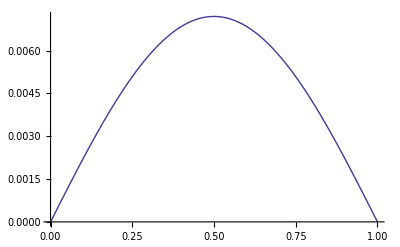

```mathematica
Plot[nsol2[x,0.5],{x,0,1}]
```

```mathematica
(* soluzione esatta *)
```

```mathematica
nexact2[x_,t_,u0_,L_,D_]=Sin[π/L x] Exp[-D π^2/L^2 t];
```

```mathematica
Plot[nexact2[x,0.5,1,1,1],{x,0,1}]
```

-Graphics-

```mathematica
(* confronto con soluzione esatta *)
```

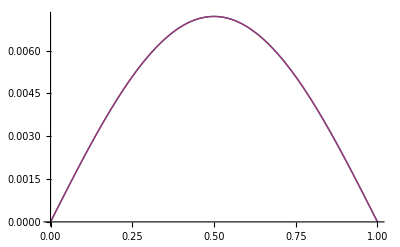

```mathematica
Plot[{nsol2[x,0.5], nexact2[x,0.5,1,1,1]},{x,0,1}]
```

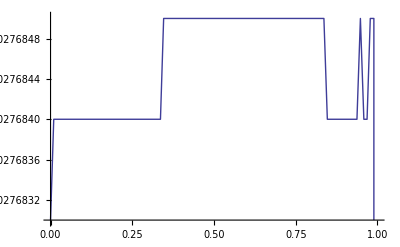

```mathematica
Plot[{nsol2[x,0.5]/ nexact2[x,0.5,1,1,1]},{x,0,1}]
```

```mathematica
(* condizione iniziale diversa (Esercizio #2) *)
```

```mathematica
(* risolviamola in un intervallo limitato con con n(0)=n(L)=0 e n(x,0) = sin( 4 π x / L) *)
```

```mathematica
inifunc3[x_,L_,u0_]=Piecewise[{{0, x== 0},{0,x==L}}, Sin[4 π x /L]];
```

```mathematica
Sol3[L_,u0_]:=Module[{},NDSolve[{pde, n[x,0]== inifunc3[x,L,u0],n[0,t]==0,n[L,t]==0},n[x,t],{x,0,L},{t,0,1.0},
MaxStepSize->1/5000][[1,1,2]]];
```

```mathematica
nsol3[x_,t_]=Sol3[1,1]
```

InterpolatingFunction[{{0.,1.},{0.,1.}},<>][x,t]

```mathematica
Plot3D[nsol3[x,t], {x,0,1},{t,0,0.05},PlotRange-> {0,1},AxesLabel->{x,t}]
```

-Graphics3D-

```mathematica
(* CONFRONTO CON CODICE DISPENSE *)
```

```mathematica
(* L = 1000
intervallo limitato con con n(0)=n(L)=0 e n(x,0) = scalino centrato 
in L/2 di larghezza 2*width dove width=100 *)
```

```mathematica
inifuncSIM[x_,L_,width_,u0_]=Piecewise[{{u0, x >= L*0.5-width && x <= L*0.5 + width}},0 ];
```

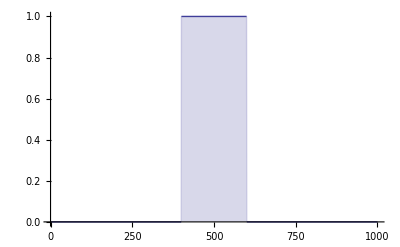

```mathematica
Plot[inifuncSIM[x,1000,100,1],{x,0,1000},Filling->Axis]
```

```mathematica
SolSIM[L_,width_,u0_]:=Module[{},NDSolve[{pde, n[x,0]== inifuncSIM[x,L,width,u0],n[0,t]==0,n[L,t]==0},n[x,t],{x,0,L},{t,0,10000.0}][[1,1,2]]];
```

```mathematica
nsolSIM[x_,t_]=SolSIM[999,100,1]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

InterpolatingFunction[{{0.,999.},{0.,10000.}},<>][x,t]

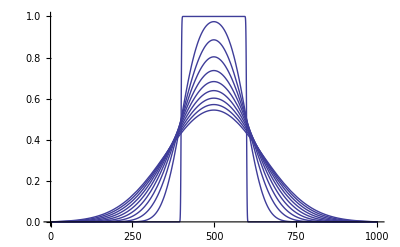

```mathematica
Plot[Table[nsolSIM[x,n],{n,1,10000,1000}],{x,0,1000}]
```

```mathematica
tbl2exp=Table[nsolSIM[x,10000],{x,0, 1000, 1}] ;
```

InterpolatingFunction::dmval: Input value {1000, 10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Export["/Users/demichel/TEMPO_DET/DIDATTICA/FISICA_COMPUTAZ_2012/LEZIONI_PRA/DIFF_EQ_E_FOURIER/fickM.dat",tbl2exp,"Data"];
```